```mathematica
<<SpinSin`
```

```mathematica
(*Parameters*)

(*our spins*)
spins={1/2};
(*exchange between spins*)
Jc1=-1;
(*exchanges between spin and conduction electrons*)
Jl=-10*{0.1,0.1,0.1,0.1};
(*their coordinates, A*)
spinsCoo={{0,0,0},{0,3,0},{3,0,0},{3,0,3}};
(*Fermi k vector, 1/A*)
kF=1;
(*DOS on Ef, ev^-1*)
rho=0.1;
(*kB*T, meV*)
kBT=0.01
(*Planck Constant in ps*mEv*)
PlanckNorm=0.6582;
PlanckNormInv = 1./PlanckNorm;

n=Dimensions[spins][[1]];
mainJ=Sum[HeisLS[spins,{i,i+1},Jc1],{i,1,n-1}];
fieldZ=ZeemanLS[spins,1,{0.,0.,1.}];
fieldX=ZeemanLS[spins,1,{1.,0.,0.}];

sops=Table[SpinOpLS[spins,i],{i,1,n}];

ham = {mainJ+fieldZ};
HH=GetHam[ham,{}];

dim=Dimensions[HH][[1]]

confls={spins,ham,sops};
```

0.01

2

```mathematica
24^4
```

331776

```mathematica
StructFactor=Table[Sinc[kF*Norm[l1-l2]]^2//N,{l1,spinsCoo},{l2,spinsCoo}]
```

{{1.,0.00221276,0.00221276,0.0441721},{0.00221276,1.,0.0441721,0.0290248},{0.00221276,0.0441721,1.,0.00221276},{0.0441721,0.0290248,0.00221276,1.}}

```mathematica
HH//MatrixForm;
```

```mathematica
esys=Sort[Transpose[Eigensystem[HH]],#1[[1]]<#2[[1]]&];

(*operator to transform to eigenbasis*)
U=SparseArray[Transpose[esys[[1;;,2]]]];
```

```mathematica
(*transform hamiltonian for test*)
Chop[ConjugateTranspose[U].HH.U,1*^-11]
```

SparseArray[…]

```mathematica
Hdiag=SparseArray[DiagonalMatrix[esys[[1;;,1]]]];
Hdiag//MatrixForm
```

(-0.058 | 0.
0. | 0.058)

```mathematica
(*Eigenvalues (energies of unperturbed system)*)
evals=esys[[1;;,1]];
```

```mathematica
(*spin matrices in eigenbasis*)
sopsEig=Table[Chop[SparseArray[ConjugateTranspose[U].opc.U],1*^-11],{op,sops},{opc,op}]
```

{{SparseArray[…],SparseArray[…],SparseArray[…]}}

```mathematica
FieldZeig=ConjugateTranspose[U].fieldZ.U
```

SparseArray[…]

```mathematica
(*Lambda struct factor*)
LambdaSF=1./4.SparseArray[ParallelTable[

Chop[

Sum[
StructFactor[[i,j]]Jl[[j]]Jl[[i]]sopsEig[[i,a]][[n1,n2]] sopsEig[[j,a]][[m1,m2]]
,{i,1,n},{j,1,n},{a,1,3}]

,1*^-11]

,{n1,1,dim},{n2,1,dim},{m1,1,dim},{m2,1,dim}]]
```

SparseArray[…]

```mathematica
LambdaSF[[1,1]];//MatrixForm
```

Null

```mathematica
LambdaSF[[1,2]];//MatrixForm
```

Null

```mathematica
LambdaSF[[2,1]];//MatrixForm
```

Null

```mathematica
LambdaSF[[2,2]];//MatrixForm
```

Null

```mathematica
(*Deltas of energies*)
Deltas=SparseArray[Table[evals[[n1]]-evals[[n2]],{n1,1,dim},{n2,1,dim}]];
```

```mathematica
Deltas//MatrixForm
```

(0. | -0.116
0.116 | 0.)

```mathematica
FF[d_,kBT_]:=If[d==0,kBT,If[kBT==0,If[d>0,d,0],d/(1-Exp[-d/kBT ])]]
Plot3D[FF[d,kBTp],{d,-1,1},{kBTp,0,2}]
```

General::munfl: -0.999857 (-2.57007328978×10^-3037) is too small to represent as a normalized machine number; precision may be lost.

-Graphics3D-

```mathematica
Fdeltas=Map[FF[#,kBT]&,Deltas,{2}]
```

SparseArray[…]

```mathematica
MatrixForm[Fdeltas]
```

(0.01 | 1.06328×10^-6
0.116001 | 0.01)

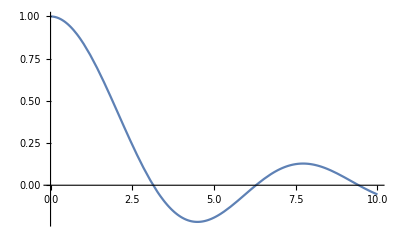

```mathematica
Plot[Sinc[d],{d,0,10}]
```

```mathematica
RR=SparseArray[{{{{0}}}},{dim,dim,dim,dim}]
```

SparseArray[…]

```mathematica
(*Table[Sum[LambdaSF[[n,npp,npp,m]]*FF[npp,kBT],{npp,1,dim}],{n,1,dim},{nmp,1,dim},{m,1,dim}]*)
```

```mathematica
(*Redfieldt=Pi rho^2 (-ReplacePart[RR,{n_,x_,m_,x_}:>TensorMultiply[LambdaSF,Fdeltas,{2,3,6}]]+
ReplacePart[RR,{n_,np_,m_,mp_}:>LambdaSF[[n,m,mp,np]]*Fdeltas[[m,n]]]-
ReplacePart[RR,{x_,np_,x_,mp_}:>Sum[LambdaSF[[mp,npp,npp,np]]*Fdeltas[[mp,npp]],{npp,1,dim}]]+
ReplacePart[RR,{n_,np_,m_,mp_}:>LambdaSF[[n,m,mp,np]]*Fdeltas[[mp,np]]]);*)
```

```mathematica
Redfield=Pi PlanckNormInv rho^2 (-ReplacePart[RR,{n_,x_,m_,x_}:>Sum[LambdaSF[[n,npp,npp,m]]*Fdeltas[[m,npp]],{npp,1,dim}]]+
ReplacePart[RR,{n_,np_,m_,mp_}:>LambdaSF[[n,m,mp,np]]*Fdeltas[[m,n]]]-
ReplacePart[RR,{x_,np_,x_,mp_}:>Sum[LambdaSF[[mp,npp,npp,np]]*Fdeltas[[mp,npp]],{npp,1,dim}]]+
ReplacePart[RR,{n_,np_,m_,mp_}:>LambdaSF[[n,m,mp,np]]*Fdeltas[[mp,np]]]);
```

```mathematica
Redfield//MatrixForm
```

((-1.26876×10^-8 | 0.
0. | 0.00138418) | (0. | -0.000811424
0. | 0.)
(0. | 0.
-0.000811424 | 0.) | (1.26876×10^-8 | 0.
0. | -0.00138418))

```mathematica
(*Convert tensor to matrix*)
MRedfield=Flatten[Redfield,{{1,2},{3,4}}]
MDeltas=Flatten[Deltas]
```

SparseArray[…]

SparseArray[…]

```mathematica
(*nn=2;
A=RandomReal[1,{nn,nn,nn,nn}];
B=RandomReal[1,{nn,nn}];*)
```

```mathematica
(*A=Array[Subscript[a,##]&,{2,2,2,2,2,2}];
TensorContract[A,{{3,5},{4,6}}]*)
```

```mathematica
(*TensorProduct[SparseArray[A],SparseArray[B],{{3,5},{4,6}}]*)
```

```mathematica
(*TensorMultiply[A,B,{{3,5},{4,6}}];*)
```

```mathematica
Redfield[[1,1]];//MatrixForm
```

Null

```mathematica
Redfield[[1,2]];//MatrixForm
```

Null

```mathematica
Redfield[[2,1]];//MatrixForm
```

Null

```mathematica
Redfield[[2,2]];//MatrixForm
```

Null

```mathematica
Fdeltas//Dimensions
LambdaSF//Dimensions
```

{12,12}

{12,12,12,12}

```mathematica
TensorMultiply[LambdaSF,Fdeltas,{2,3,6}]
```

SparseArray[…]

```mathematica
(*+ (FieldZeig.dm-dm.FieldZeig)*)
```

RHSt[SparseArray[…],SparseArray[…],SparseArray[…]]

```mathematica
aa=Array[1,1000000];
```

```mathematica
ArrayReshape[aa,{1000,1000}]
```

{1}
 |  |  |  |

```mathematica
TensorMultiply[A_,B_,pairs_]:=Activate@TensorContract[Inactive[TensorProduct][A,B],pairs];

(*Acting of Renfield operator on density matrix*)
RedfieldRHSt[R_,dm_]:=TensorMultiply[R,dm,{{3,5},{4,6}}]

(*Right Hand Side part of time dependent QME *)
RHStd[ham_,R_,dm_]:=-ⅈ PlanckNormInv (ham.dm-dm.ham )+RedfieldRHSt[R,dm]

RungeKuttaStepDMRtd[dm_,ham_,redfield_,time_,step_]:=
Module[{k1,k2,k3,k4},
k1=RHStd[ham[time],redfield,dm];
k2=RHStd[ham[time+0.5*step],redfield,dm+k1 *step*0.5];
k3=RHStd[ham[time+0.5*step],redfield,dm+k2 *step*0.5];
k4=RHStd[ham[time+step],redfield,dm+k3 *step];
Return[1./6.(k1+2.0 k2+2.0 k3 + k4)];
]
```

RHSt[SparseArray[…],SparseArray[…],SparseArray[…]]

```mathematica
RungeKuttaStepDMRM[dm_,step_]:=
Module[{k1,k2,k3,k4},
k1=MRHSt[MDeltas,MRedfield,dm];
k2=MRHSt[MDeltas,MRedfield,dm+k1 *step/2.];
k3=MRHSt[MDeltas,MRedfield,dm+k2 *step/2.];
k4=MRHSt[MDeltas,MRedfield,dm+k3 *step];
Return[1./6.(k1+2.0 k2+2.0 k3 + k4)];
]

RungeKuttaStepDMR[dm_,step_]:=
Module[{k1,k2,k3,k4},
k1=RHSt[Deltas,Redfield,dm];
k2=RHSt[Deltas,Redfield,dm+k1 *step/2.];
k3=RHSt[Deltas,Redfield,dm+k2 *step/2.];
k4=RHSt[Deltas,Redfield,dm+k3 *step];
Return[1./6.(k1+2.0 k2+2.0 k3 + k4)];
]

(*Right Hand Side part of time dependent QME *)
RHSt[d_,R_,dm_]:=-ⅈ PlanckNormInv (d*dm )+RedfieldRHSt[R,dm]



(*Matrix Form RHS, dm, d - vectors, R - matrix Redfield operator*)
MRHSt[d_,restHam_,R_,dm_]:=-ⅈ (PlanckNormInv (d*dm ) (*+ restHam.*))+MRedfield.dm
```

```mathematica
dm=SparseArray[{{0}},{dim,dim}];
dm[[2,2]]=1;
RHSt[Deltas,Redfield,dm]
```

SparseArray[…]

```mathematica
r2[[3,3]]//MatrixForm
```

0.011573

```mathematica
Redfield//MatrixForm
```

((0. | 0. | 6.91691×10^-6 | 0.
0. | 0.0114226 | 0. | 0.
6.91691×10^-6 | 0. | 0.0115681 | 0.
0. | 0. | 0. | 0.0117587) | (0. | -0.0058179 | 0. | 0.
0. | 0. | 0. | 0.
0. | 0.000175074 | 0. | 0.
-0.00586145 | 0. | -0.000712176 | 0.) | (0. | 0. | -0.00640471 | 0.
0. | -0.00051659 | 0. | 0.
0.00578407 | 0. | 0.000343231 | 0.
0. | 0. | 0. | -0.000539279) | (0. | 0. | 0. | -0.00658544
-0.00569393 | 0. | -0.000681942 | 0.
0. | 0. | 0. | 0.000175074
0. | 0. | 0. | 0.)
(0. | 0. | 0. | -0.00586145
-0.0058179 | 0. | 0.000175074 | 0.
0. | 0. | 0. | -0.000712176
0. | 0. | 0. | 0.) | (6.643×10^-174 | 0. | -7.7305×10^-6 | 0.
0. | -0.0114261 | 0. | 0.
-7.7305×10^-6 | 0. | 0.00123722 | 0.
0. | 0. | 0. | 0.) | (0. | 0. | 0. | -9.91827×10^-6
4.19169×10^-7 | 0. | -0.0122226 | 0.
0. | 0. | 0. | 0.00121977
0. | 0. | 0. | 0.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | -0.012613
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(-2.71523×10^-178 | 0. | 0.00578407 | 0.
0. | -0.00051659 | 0. | 0.
-0.00640471 | 0. | 0.000343231 | 0.
0. | 0. | 0. | -0.000539279) | (0. | 4.19169×10^-7 | 0. | 0.
0. | 0. | 0. | 0.
0. | -0.0122226 | 0. | 0.
-9.91827×10^-6 | 0. | 0.00121977 | 0.) | (1.87257×10^-176 | 0. | 8.38338×10^-7 | 0.
0. | 3.44367×10^-6 | 0. | 0.
8.38338×10^-7 | 0. | -0.0128093 | 0.
0. | 0. | 0. | 0.00120247) | (0. | 0. | 0. | 4.19169×10^-7
-2.84042×10^-8 | 0. | 3.70157×10^-6 | 0.
0. | 0. | 0. | -0.0129901
0. | 0. | 0. | 0.)
(0. | -0.00569393 | 0. | 0.
0. | 0. | 0. | 0.
0. | -0.000681942 | 0. | 0.
-0.00658544 | 0. | 0.000175074 | 0.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | -0.012613 | 0. | 0.) | (0. | -2.84042×10^-8 | 0. | 0.
0. | 0. | 0. | 0.
0. | 3.70157×10^-6 | 0. | 0.
4.19169×10^-7 | 0. | -0.0129901 | 0.) | (6.26817×10^-179 | 0. | -2.47426×10^-8 | 0.
0. | 0. | 0. | 0.
-2.47426×10^-8 | 0. | 3.95989×10^-6 | 0.
0. | 0. | 0. | -0.0129611))

-0.0000186844

```mathematica
NumericArrayQ[{2.,2.}]
```

False

```mathematica
purged2 = SparseArray[Table[ 
ind=Keys[rule];
If[ 
Abs[Deltas[[ind[[1]],ind[[2]]]]-Deltas[[ind[[3]],ind[[4]]]]] < kBT,
rule,
ind->0
]
,{rule,ArrayRules[Redfield]}]];
```

Part::pkspec1: The expression _ cannot be used as a part specification.

```mathematica
purged2//MatrixForm
```

((0. | 0. | 0. | 0.
0. | 0.0114226 | 0. | 0.
0. | 0. | 0.0115681 | 0.
0. | 0. | 0. | 0.0117587) | (0. | -0.0058179 | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (0. | 0. | -0.00640471 | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (0. | 0. | 0. | -0.00658544
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(0. | 0. | 0. | 0.
-0.0058179 | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (6.643×10^-174 | 0. | 0. | 0.
0. | -0.0114261 | 0. | 0.
0. | 0. | 0.00123722 | 0.
0. | 0. | 0. | 0.) | (0. | 0. | 0. | 0.
0. | 0. | -0.0122226 | 0.
0. | 0. | 0. | 0.00121977
0. | 0. | 0. | 0.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | -0.012613
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
-0.00640471 | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | -0.0122226 | 0. | 0.
0. | 0. | 0.00121977 | 0.) | (1.87257×10^-176 | 0. | 0. | 0.
0. | 3.44367×10^-6 | 0. | 0.
0. | 0. | -0.0128093 | 0.
0. | 0. | 0. | 0.00120247) | (0. | 0. | 0. | 0.
0. | 0. | 3.70157×10^-6 | 0.
0. | 0. | 0. | -0.0129901
0. | 0. | 0. | 0.)
(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
-0.00658544 | 0. | 0. | 0.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | -0.012613 | 0. | 0.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 3.70157×10^-6 | 0. | 0.
0. | 0. | -0.0129901 | 0.) | (6.26817×10^-179 | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 3.95989×10^-6 | 0.
0. | 0. | 0. | -0.0129611))

```mathematica
(*(*Redfield in Matrix Form, DM in vector*)
pdt=MaxTime/(Dimensions[ParValList][[2]]-1);
TimeArr=Table[pdt*(it-1),{it,1,Dimensions[ParValList][[2]]}];
Parameters=Map[Interpolation[Transpose[{TimeArr,#}]]&,ParValList];
ParamsF[lt_]:=Map[#[lt]&,Parameters];*)
```

```mathematica
maxTime=1000;

dmm=SparseArray[{{0}},{dim,dim}];
dmm[[2,2]]=1;

dm=Flatten[dmm];

step=0.1;
dms={};
numSteps=IntegerPart[maxTime/step];

Timing[
Table[
dmn=dm+step*RungeKuttaStepDMRM[dm,step];
dm=dmn;
AppendTo[dms,dm];
tr=Tr[dm];
If[Abs[tr-1]>1.10^-11,Print["Error! Trace differs from 1, decrease step. Abortion!"];Abort[];];
,{i,1,numSteps}];]
```

$Aborted

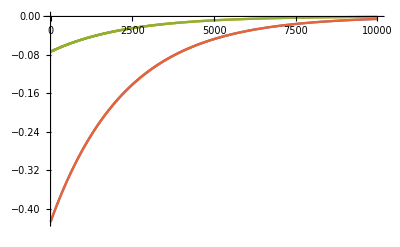

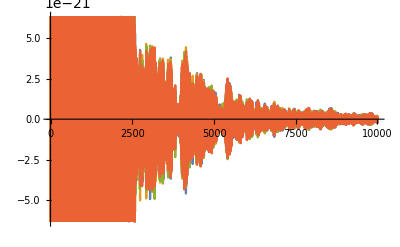

```mathematica
spinvals=Table[Tr[sop.ArrayReshape[dm,{dim,dim}]],{spn,sopsEig},{sop,spn},{dm,dms}];
ListLinePlot[spinvals[[;;,3]],PlotRange->All]
ListLinePlot[spinvals[[;;,1]]]
```

```mathematica
Evals=Table[Tr[Hdiag.dm],{dm,dms}];
```

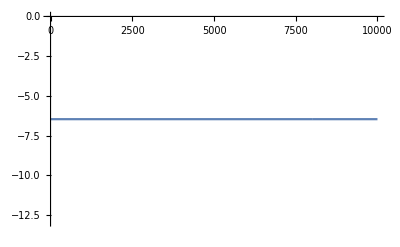

```mathematica
ListLinePlot[Evals,PlotRange->All]
```

```mathematica
maxTime=1000;

dm=SparseArray[{{0}},{dim,dim}];
dm[[2,2]]=1;


step=0.1;
dms={};
numSteps=IntegerPart[maxTime/step];

Timing[
Table[
dmn=dm+step*RungeKuttaStepDMR[dm,step];
dm=dmn;
AppendTo[dms,dm];
tr=Tr[dm];
If[Abs[tr-1]>1.10^-11,Print["Error! Trace differs from 1, decrease step. Abortion!"];Abort[];];
,{i,1,numSteps}];]
```

{7.64172,Null}

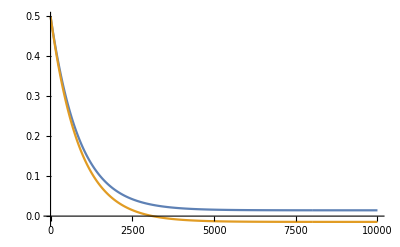

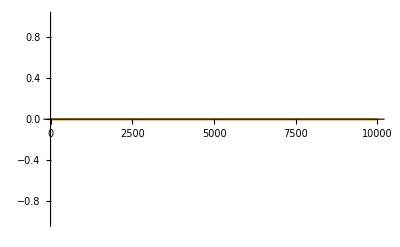

```mathematica
spinvals=Table[Tr[sop.dm],{spn,sopsEig},{sop,spn},{dm,dms}];
ListLinePlot[spinvals[[;;,3]],PlotRange->All]
ListLinePlot[spinvals[[;;,1]]]
```

```mathematica
Tr[dm]
Chop[dm,0.0000001]//MatrixForm
```

1.

```mathematica
Table[Tr[sopsEig[[i,j]].dm],{i,1,3},{j,1,n}]//Transpose//MatrixForm
```

Part::partw: Part 4 of {SparseArray[«1»],SparseArray[Automatic,«3»],SparseArray[Automatic,«3»]} does not exist.

Part::partw: Part 4 of {«1»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

(0. | 0. | 0.
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.0180259 | -0.0154374 | 0.00836552
Tr[{{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]}}⟦1,4⟧.SparseArray[…]] | Tr[{{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]}}⟦2,4⟧.SparseArray[…]] | Tr[{{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]}}⟦3,4⟧.SparseArray[…]])